```mathematica
traindata=ExampleData[{"MachineLearning","MNIST"},"TrainingData"];
```

```mathematica
mtestset=ExampleData[{"MachineLearning","MNIST"},"TestData"];
```

```mathematica
indexs=Table[i,{i,1,Length[traindata]}];
indexs=RandomSample[indexs];
mvalidset=traindata[[indexs[[1;;10000]]]];
mtrainset=traindata[[indexs[[10001;;60000]]]];
```

```mathematica
mtrainset[[1,1]]
```

-Graphics-

Naive Bayes Classifieur:
On entraîne le classifieur sur l’ensemble d’entraîinement et évalue le performance sur l’ensemble mtrainset, mtestset.

```mathematica
c=Classify[mtrainset,Method->"NaiveBayes"]
```

ClassifierFunction[…]

```mathematica
ClassifierInformation[c]
```

Classifier information
Input type | Image
Number of classes | 10
Method | NaiveBayes
Accuracy | 84. % ± 0.46 %
Loss | 4.57 ± 0.2
Evaluation time | 140. µs/example
Classifier memory | 3.93 MB
Training examples used | 50000 examples
Training time | 55.1 s
 |

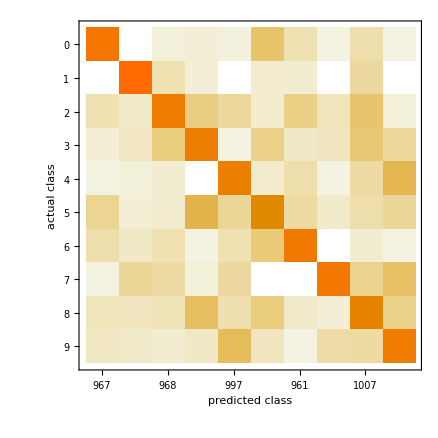
{0.1551,-Graphics-}

```mathematica
ClassifierMeasurements[c, mtestset,{"Error","ConfusionMatrixPlot"}]
```

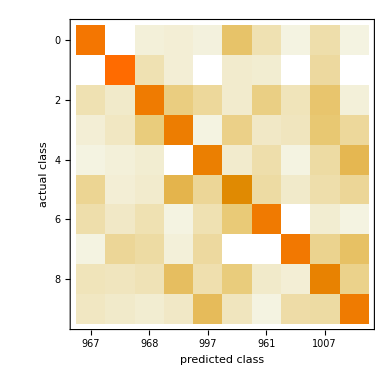
{-47767.4,-Graphics-}

```mathematica
ClassifierMeasurements[c, mtestset,{"LogLikelihood","ConfusionMatrixPlot"}]
```

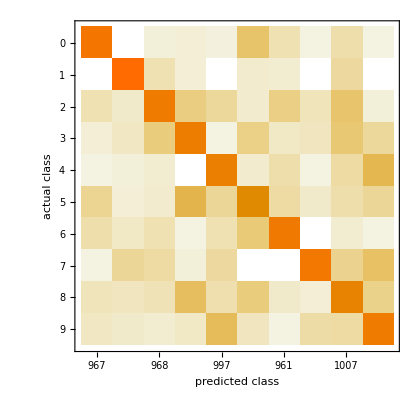
{4.77674,-Graphics-}

```mathematica
ClassifierMeasurements[c, mtestset,{"MeanCrossEntropy","ConfusionMatrixPlot"}]
```

On cherche le optimal hyper parameter SmoothingParameter sur l’ensemble de validation mvalidset.  On entraîne le classifieur sur l’ensemble d’entraîinement et évalue le performance sur l’ensemble mtrainset, mvalidset.

```mathematica
{c2,c3,c4,c5,c6}=Classify[mtrainset, Method->{"NaiveBayes","SmoothingParameter"->#}]&/@{.2,.5,2,20,40};
```

```mathematica
Print ["training error:"]
ClassifierMeasurements[c2, mtrainset,{"Error"}]
ClassifierMeasurements[c3, mtrainset,{"Error"}]
ClassifierMeasurements[c4, mtrainset,{"Error"}]
ClassifierMeasurements[c5, mtrainset,{"Error"}]
ClassifierMeasurements[c6, mtrainset,{"Error"}]

Print ["validation error:"]
ClassifierMeasurements[c2, mvalidset,{"Error"}]
ClassifierMeasurements[c3, mvalidset,{"Error"}]
ClassifierMeasurements[c4, mvalidset,{"Error"}]
ClassifierMeasurements[c5, mvalidset,{"Error"}]
ClassifierMeasurements[c6, mvalidset,{"Error"}]
```

training error:

{0.15468}

{0.15482}

{0.15524}

{0.15704}

{0.1581}

validation error:

{0.1669}

{0.167}

{0.1672}

{0.1688}

{0.1705}

Résumer: l’erreur de validation augmente et l’erreur d’entraîinement aussi augmente. 
Donc, le SmoothingParameter optimal est .2, on évalue le performance sur ensemble de test.

```mathematica
ClassifierMeasurements[c2, mtestset,{"Error"}]
```

{0.1538}

```mathematica
SupportVectorMachine Classifieur:
```

On entraîne le classifieur sur l’ensemble d’entraîinement et évalue le performance sur l’ensemble mtrainset, mtestset.

```mathematica
c1=Classify[mtrainset,Method->{"SupportVectorMachine", "KernelType"->"Linear"}]
```

ClassifierFunction[…]

```mathematica
ClassifierInformation[c1]
```

Classifier information
Input type | Image
Number of classes | 10
Method | SupportVectorMachine
Accuracy | 92.8 % ± 0.17 %
Loss | 0.329 ± 0.0098
Evaluation time | 283. µs/example
Classifier memory | 137. MB
Training examples used | 50000 examples
Training time | 17 1
 |

```mathematica
c2=Classify[mtrainset,Method->{"SupportVectorMachine", "KernelType"->"RadialBasisFunction"}]
```

ClassifierFunction[…]

```mathematica
ClassifierInformation[c2]
```

Classifier information
Input type | Image
Number of classes | 10
Method | SupportVectorMachine
Accuracy | 90.6 % ± 0.67 %
Loss | 0.34 ± 0.025
Evaluation time | 734. µs/example
Classifier memory | 223. MB
Training examples used | 50000 examples
Training time | 29 22
 |

```mathematica
c3=Classify[mtrainset,Method->{"SupportVectorMachine", "KernelType"->"Polynomial"}]
```

ClassifierFunction[…]

```mathematica
ClassifierInformation[c3]
```

Classifier information
Input type | Image
Number of classes | 10
Method | SupportVectorMachine
Accuracy | 95.9 % ± 0.2 %
Loss | 0.187 ± 0.012
Evaluation time | 675. µs/example
Classifier memory | 119. MB
Training examples used | 50000 examples
Training time | 13 42
 |

On évalue le performance sur l’ensemble mtrainset, mtestset.

```mathematica
Print["training error:"]
ClassifierMeasurements[c1, mtrainset,{"Error"}]
ClassifierMeasurements[c2, mtrainset,{"Error"}]
ClassifierMeasurements[c3, mtrainset,{"Error"}]
```

training error:

{0.0387}

{0.04666}

{0.02694}

```mathematica
Print["test error:"]
ClassifierMeasurements[c1, mtestset,{"Error"}]
ClassifierMeasurements[c2, mtestset,{"Error"}]
ClassifierMeasurements[c3, mtestset,{"Error"}]
```

test error:

{0.0541}

{0.0484}

{0.0388}

Donc, l’erreur de test diminue. Le kernel type polynomial est le meilleur classifieur. On va chercher le optimal hyper parameter sur l’ensemble validation.
On entraîne le classifieur pour PolynomiaDegree 3,4,5,9

```mathematica
{c4,c5,c6,c7}=Classify[mtrainset, Method->{"SupportVectorMachine", "KernelType"->"Polynomial","PolynomialDegree"->#}]&/@{3,4,5,9};
```

On évalue le performance sur l’ensemble de validation.

```mathematica
Print["validation error:"]
ClassifierMeasurements[c4, mvalidset,{"Error"}]
ClassifierMeasurements[c5, mvalidset,{"Error"}]
ClassifierMeasurements[c6, mvalidset,{"Error"}]
ClassifierMeasurements[c7, mvalidset,{"Error"}]
```

validation error:

{0.0397}

{0.0314}

{0.0257}

{0.0234}

Donc, l’erreur de validation diminue. Le degrè 9 est le meilleur hyper paramètre. On va chercher le optimal GammaScalingParameter parameter sur l’ensemble validation.

On entraîne le classifieur pour GammaScalingParameter .0001

```mathematica
c8=Classify[mtrainset, Method->{"SupportVectorMachine", "KernelType"->"Polynomial","PolynomialDegree"->9, "GammaScalingParameter"-> 0.0001}]
```

ClassifierFunction[…]

On entraîne le classifieur pour GammaScalingParameter .001

```mathematica
c9=Classify[mtrainset, Method->{"SupportVectorMachine", "KernelType"->"Polynomial","PolynomialDegree"->9, "GammaScalingParameter"-> 0.001}]
```

ClassifierFunction[…]

On entraîne le classifieur pour GammaScalingParameter .01

```mathematica
c10=Classify[mtrainset, Method->{"SupportVectorMachine", "KernelType"->"Polynomial","PolynomialDegree"->9, "GammaScalingParameter"-> 0.01}]
```

ClassifierFunction[…]

On entraîne le classifieur pour GammaScalingParameter .1

```mathematica
c11=Classify[mtrainset, Method->{"SupportVectorMachine", "KernelType"->"Polynomial","PolynomialDegree"->9, "GammaScalingParameter"-> 0.1}]
```

ClassifierFunction[…]

On entraîne le classifieur pour GammaScalingParameter 1

```mathematica
c12=Classify[mtrainset, Method->{"SupportVectorMachine", "KernelType"->"Polynomial","PolynomialDegree"->9, "GammaScalingParameter"-> 1}]
```

ClassifierFunction[…]

On entraîne le classifieur pour GammaScalingParameter 10

```mathematica
c13=Classify[mtrainset, Method->{"SupportVectorMachine", "KernelType"->"Polynomial","PolynomialDegree"->9, "GammaScalingParameter"-> 10}]
```

ClassifierFunction[…]

```mathematica
Print["validation error:"]
ClassifierMeasurements[c8, mvalidset,{"Error"}]
ClassifierMeasurements[c9, mvalidset,{"Error"}]
ClassifierMeasurements[c10, mvalidset,{"Error"}]
ClassifierMeasurements[c11, mvalidset,{"Error"}]
ClassifierMeasurements[c12, mvalidset,{"Error"}]
ClassifierMeasurements[c13, mvalidset,{"Error"}]
```

validation error:

{0.0578}

{0.0223}

{0.0183}

{0.0184}

{0.018}

{0.018}

l’erreur de validation diminue pour Gamma 1.  Donc, le Gamma optimal est 1
on évalue le performance sur ensemble de test.

test error:

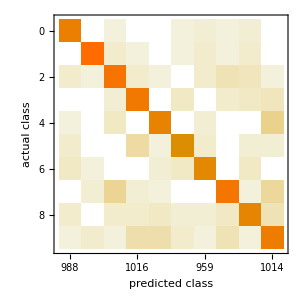
{0.0196,-Graphics-}

```mathematica
Print["test error:"]
ClassifierMeasurements[c12, mtestset,{"Error","ConfusionMatrixPlot"}]
```

```mathematica
Remove[traindata]
```

```mathematica
(* CIFAR-10 *)
obj=ResourceObject["CIFAR-10"]
```

ResourceObject[…]

```mathematica
traindata=ResourceData[obj,"TrainingData"];
ctestset=ResourceData[obj,"TestData"];
indexs=Table[i,{i,1,Length[traindata]}];
indexs=RandomSample[indexs];
cvalidset = traindata[[indexs[[1;;2000]]]];
ctrainset = traindata[[indexs[[2001;;12000]]]];
```

```mathematica
data2 = ColorConvert[Table[cvalidset[[i,1]],{i,1,2000}],"Grayscale"];
data3= ColorConvert[Table[ctrainset[[i,1]],{i,1,10000}],"Grayscale"];
```

```mathematica
data4=ColorConvert[Table[ctestset[[i,1]],{i,1,10000}],"Grayscale"];
```

```mathematica
cvalidset =Table[data2[[i]]->cvalidset[[i,2]],{i,1,2000}];
```

```mathematica
ctrainset = Table[data3[[i]]->ctrainset[[i,2]],{i,1,10000}];
```

```mathematica
ctestset= Table[data4[[i]]->ctestset[[i,2]],{i,1,10000}];
```

Naive Bayes Classifieur:
On entraîne le classifieur sur l’ensemble d’entraîinement et évalue le performance sur l’ensemble ctrainset, ctestset.

```mathematica
c=Classify[ctrainset,Method->"NaiveBayes"]
```

ClassifierFunction[…]

```mathematica
ClassifierInformation[c]
```

Classifier information
Input type | Image
Number of classes | 10
Method | NaiveBayes
Accuracy | 26.1 % ± 0.98 %
Loss | 100. ± 2.8
Evaluation time | 140. µs/example
Classifier memory | 16.8 MB
Training examples used | 10000 examples
Training time | 31.5 s
 |

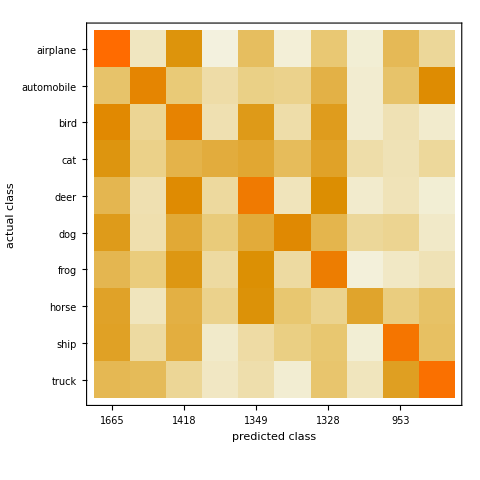
{0.7363,-Graphics-}

```mathematica
ClassifierMeasurements[c, ctestset,{"Error","ConfusionMatrixPlot"}]
```

On cherche le optimal hyper parameter SmoothingParameter sur l’ensemble de validation cvalidset.  On entraîne le classifieur sur l’ensemble d’entraîinement et évalue le performance sur l’ensemble ctrainset, cvalidset.

```mathematica
{c2,c3,c4,c5,c6}=Classify[ctrainset, Method->{"NaiveBayes","SmoothingParameter"->#}]&/@{.2,.5,2,20,40};
```

```mathematica
Print ["training error:"]
ClassifierMeasurements[c2, ctrainset,{"Error"}]
ClassifierMeasurements[c3, ctrainset,{"Error"}]
ClassifierMeasurements[c4, ctrainset,{"Error"}]
ClassifierMeasurements[c5, ctrainset,{"Error"}]
ClassifierMeasurements[c6, ctrainset,{"Error"}]

Print ["validation error:"]
ClassifierMeasurements[c2, cvalidset,{"Error"}]
ClassifierMeasurements[c3, cvalidset,{"Error"}]
ClassifierMeasurements[c4, cvalidset,{"Error"}]
ClassifierMeasurements[c5, cvalidset,{"Error"}]
ClassifierMeasurements[c6, cvalidset,{"Error"}]
```

training error:

{0.5777}

{0.5783}

{0.5784}

{0.5791}

{0.5797}

validation error:

{0.74}

{0.7405}

{0.7405}

{0.74}

{0.7405}

Résumer: l’erreur de validation augmente et l’erreur d’entraîinement aussi augmente. 
Donc, le SmoothingParameter optimal est .2, on évalue le performance sur ensemble de test.

```mathematica
ClassifierMeasurements[c2, ctestset,{"Error","ConfusionMatrixPlot"}]
```

{0.7363,-Graphics-}

SupportVectorMachine Classifieur:
On entraîne le classifieur sur l’ensemble d’entraîinement et évalue le performance sur l’ensemble ctrainset, ctestset.

```mathematica
c2=Classify[ctrainset,Method->{"SupportVectorMachine", "KernelType"->"Linear"}]
```

ClassifierFunction[…]

```mathematica
ClassifierInformation[c2]
```

Classifier information
Input type | Image
Number of classes | 10
Method | SupportVectorMachine
Accuracy | 9.66 % ± 0.4 %
Loss | 2.67 ± 0.015
Evaluation time | 169. µs/example
Classifier memory | 434. MB
Training examples used | 10000 examples
Training time | 12 12
 |

```mathematica
c3=Classify[ctrainset,Method->{"SupportVectorMachine", "KernelType"->"RadialBasisFunction"}]
```

ClassifierFunction[…]

```mathematica
ClassifierInformation[c3]
```

Classifier information
Input type | Image
Number of classes | 10
Method | SupportVectorMachine
Accuracy | 9.94 % ± 1.1 %
Loss | 2.35 ± 0.014
Evaluation time | 568. µs/example
Classifier memory | 717. MB
Training examples used | 10000 examples
Training time | 18 48
 |

```mathematica
c4=Classify[ctrainset,Method->{"SupportVectorMachine", "KernelType"->"Polynomial"}]
```

ClassifierFunction[…]

On évalue le performance sur l’ensemble ctrainset, ctestset.

```mathematica
Print["training error:"]
ClassifierMeasurements[c2, ctrainset,{"Error"}]
ClassifierMeasurements[c3, ctrainset,{"Error"}]
ClassifierMeasurements[c4, ctrainset,{"Error"}]

Print["test error:"]
ClassifierMeasurements[c2, ctestset,{"Error"}]
ClassifierMeasurements[c3, ctestset,{"Error"}]
ClassifierMeasurements[c4, ctestset,{"Error"}]
```

training error:

{0.5469}

{0.8272}

{0.7524}

test error:

{0.782}

{0.8213}

{0.7502}

Donc, l’erreur de test diminue. Le kernel type polynomial est le meilleur classifieur. On va chercher le optimal hyper parameter sur l’ensemble validation.
On entraîne le classifieur pour PolynomiaDegree 3,4,5,9

```mathematica
{c5,c6,c7,c8}=Classify[ctrainset, Method->{"SupportVectorMachine", "KernelType"->"Polynomial","PolynomialDegree"->#}]&/@{3,4,5,9};
```

On évalue le performance sur l’ensemble de validation.

```mathematica
Print["validation error:"]
ClassifierMeasurements[c5, cvalidset,{"Error"}]
ClassifierMeasurements[c6, cvalidset,{"Error"}]
ClassifierMeasurements[c7, cvalidset,{"Error"}]
ClassifierMeasurements[c8, cvalidset,{"Error"}]
```

validation error:

{0.75}

{0.845}

{0.7495}

{0.7375}

Donc, l’erreur de validation diminue. Le degrè 9 est le meilleur hyper paramètre. On va chercher le optimal GammaScalingParameter parameter sur l’ensemble validation.
On entraîne le classifieur pour GammaScalingParameter .0001

```mathematica
c13=Classify[ctrainset, Method->{"SupportVectorMachine", "KernelType"->"Polynomial","PolynomialDegree"->9, "GammaScalingParameter"-> 0.0001}]
```

ClassifierFunction[…]

On entraîne le classifieur pour GammaScalingParameter .001

```mathematica
c9=Classify[ctrainset, Method->{"SupportVectorMachine", "KernelType"->"Polynomial","PolynomialDegree"->9, "GammaScalingParameter"-> 0.001}]
```

ClassifierFunction[…]

On entraîne le classifieur pour GammaScalingParameter .01

```mathematica
c12=Classify[ctrainset, Method->{"SupportVectorMachine", "KernelType"->"Polynomial","PolynomialDegree"->9, "GammaScalingParameter"-> 0.01}]
```

ClassifierFunction[…]

On entraîne le classifieur pour GammaScalingParameter 1

```mathematica
c10=Classify[ctrainset, Method->{"SupportVectorMachine", "KernelType"->"Polynomial","PolynomialDegree"->9, "GammaScalingParameter"-> 1}]
```

ClassifierFunction[…]

On entraîne le classifieur pour GammaScalingParameter 10

```mathematica
c11=Classify[ctrainset, Method->{"SupportVectorMachine", "KernelType"->"Polynomial","PolynomialDegree"->9, "GammaScalingParameter"-> 10}]
```

ClassifierFunction[…]

```mathematica
Print["validation error:"]
ClassifierMeasurements[c13, cvalidset,{"Error"}]
ClassifierMeasurements[c9, cvalidset,{"Error"}]
ClassifierMeasurements[c12, cvalidset,{"Error"}]
ClassifierMeasurements[c10, cvalidset,{"Error"}]
ClassifierMeasurements[c11, cvalidset,{"Error"}]
```

validation error:

{0.736}

{0.678}

{0.7155}

{0.776}

{0.7965}

l’erreur de validation diminue pour Gamma .001.  Donc, le Gamma optimal est .001
on évalue le performance sur ensemble de test.

test error:

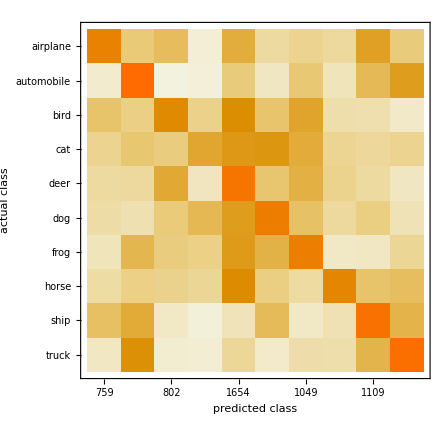
{0.6655,-Graphics-}

```mathematica
Print["test error:"]
ClassifierMeasurements[c9, ctestset,{"Error","ConfusionMatrixPlot"}]
```